```mathematica
14 12
```

168

```mathematica
CONTROLLER.mouseController.pressed_M(new Point(2,5));
CONTROLLER.mouseController.dragged_M(new Point(1,5));
CONTROLLER.mouseController.dragged_M(new Point(1,10));
CONTROLLER.mouseController.dragged_M(new Point(12,5));
CONTROLLER.mouseController.dragged_M(new Point(2,5));
CONTROLLER.mouseController.released_M();

CONTROLLER.mouseController.pressed_M(new Point(3,0));
CONTROLLER.mouseController.dragged_M(new Point(3,7));
CONTROLLER.mouseController.released_M();
```

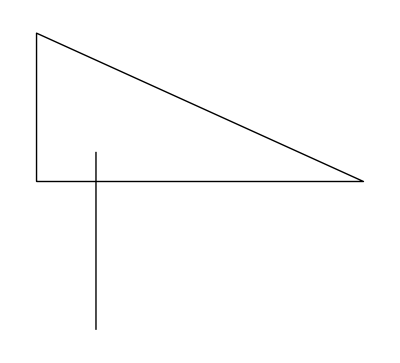

```mathematica
Graphics[{Line[{{1,5},{1,10},{12,5},{1,5}}],Line[{{3,0},{3,6}}]}]
```

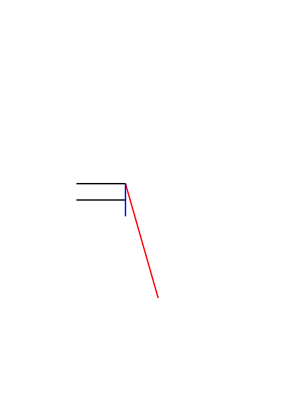

```mathematica
Graphics[{Red,Line[{{21,11},{23,4}}],Black,Line[{{18,11},{21,11}}],Line[{{18,10},{21,10}}],Blue,Line[{{21,11},{21,10}}],Line[{{21,10},{21,9}}]},PlotRange->{{15,30},{0,20}}]
```

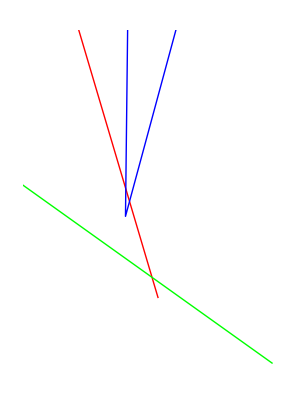

```mathematica
Graphics[{Red,Line[{{7,58},{23,4}}],Green,Line[{{30,0},{9,15}}],Blue,Line[{{22,96},{21,12}}]{21,9},{44,94}}]},PlotRange->{{15,30},{0,20}}]
```

[PTBA: <815.0, 365.0> 0.0, PTBA: <815.375, 364.75> 0.041666666666666664, PTBA: <824.0, 359.0> 1.0]

```mathematica
12+0.4375(1-12)
```

7.1875

### before

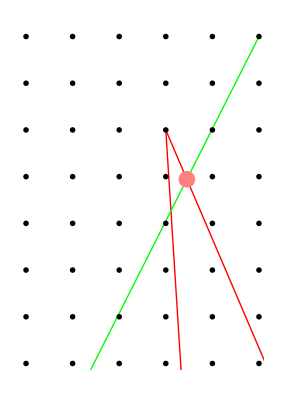

```mathematica
Graphics[{Red,Line[{{73,26},{43,96},{46,49}}],Green,Line[{{45,98},{5,19}}],Pink,PointSize[0.03],Point[{43.4526,94.94390}],Black,PointSize[0.01],Table[Point[{i,j}],{i,40,50},{j,90,100}]},PlotRange->{{43-3,43+2},{96-5,96+2}}]
```

### after

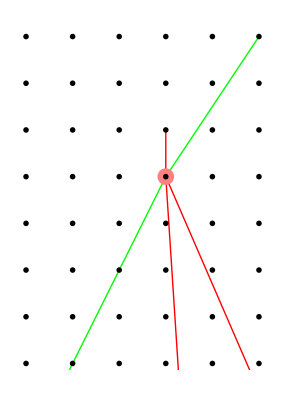

```mathematica
Graphics[{Red,Line[{{43,96},{43,95},{46,49}}],Line[{{43,95},{73,26}}],Green,Line[{{45,98},{43,95}}],Line[{{43,95},{5,19}}],Pink,PointSize[0.03],Point[{43,95}],Black,PointSize[0.01],Table[Point[{i,j}],{i,40,50},{j,90,100}]},PlotRange->{{43-3,43+2},{96-5,96+2}}]
```

### before

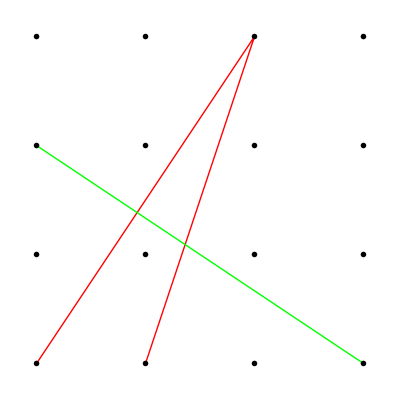

```mathematica
Graphics[{Red,Line[{{0,0},{2, 3},{1,0}}],Green,Line[{{3,0},{0,2}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,0,3},{j,0,3}]}]
```

### before

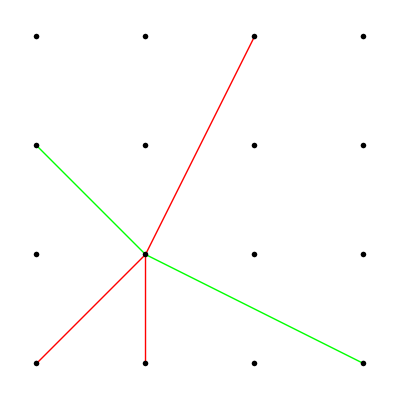

```mathematica
Graphics[{Red,Line[{{0,0},{1,1}}],Line[{{1,1},{2, 3}}],Line[{{1,1},{1,0}}],Green,Line[{{3,0},{1,1},{0,2}}],Black,PointSize[0.01],Table[Point[{i,j}],{i,0,3},{j,0,3}]}]
```